#### Computation of a*=f(N)

Actually, the second solution would just gives a off result over the whole plane, which is not physically relevant.

#### 1) 1st method using discriminant

```mathematica
ClearAll[a,kb,ka,μ,η,lambdaa,lambdab,n,astar,λa,λb,ka,kb,a];

g[a_,n_]:=kb*μ*a^3+(μ+kb*η)a^2+(η-λb-kb*n)a-n
```

```mathematica
poly=Expand[g[a,n]];
poly//TraditionalForm
```

a^3 kb μ+a^2 η kb+a^2 μ+a η-a kb n-a λb-n

```mathematica
disc=FullSimplify[Discriminant[poly,a]];
Print["The discriminant of the y polynomial is Δ = ",disc];
```

The discriminant of the y polynomial is Δ = kb^4 n^2 (η^2+4 n μ)+μ^2 ((η-λb)^2+4 n μ)+2 kb^3 n (η^3+η^2 λb+4 n η μ+6 n λb μ)+2 kb μ (-((η-2 λb) (η-λb)^2)+2 n (-2 η+5 λb) μ)+kb^2 (η^2 (η-λb)^2+2 n (η^2-η λb+6 λb^2) μ-8 n^2 μ^2)

```mathematica
solution=Solve[g[a,n]==0,a]
```

{{a→-(kb η+μ)/(3 kb μ)-(2^(1/3) (3 kb (-kb n+η-λb) μ-(kb η+μ)^2))/(3 kb μ (-2 kb^3 η^3-9 kb^3 n η μ+3 kb^2 η^2 μ-9 kb^2 η λb μ+18 kb^2 n μ^2+3 kb η μ^2-9 kb λb μ^2-2 μ^3+√((-2 kb^3 η^3-9 kb^3 n η μ+3 kb^2 η^2 μ-9 kb^2 η λb μ+18 kb^2 n μ^2+3 kb η μ^2-9 kb λb μ^2-2 μ^3)^2+4 (3 kb (-kb n+η-λb) μ-(kb η+μ)^2)^3))^(1/3))+1/(3 2^(1/3) kb μ)(-2 kb^3 η^3-9 kb^3 n η μ+3 kb^2 η^2 μ-9 kb^2 η λb μ+18 kb^2 n μ^2+3 kb η μ^2-9 kb λb μ^2-2 μ^3+√((-2 kb^3 η^3-9 kb^3 n η μ+3 kb^2 η^2 μ-9 kb^2 η λb μ+18 kb^2 n μ^2+3 kb η μ^2-9 kb λb μ^2-2 μ^3)^2+4 (3 kb (-kb n+η-λb) μ-(kb η+μ)^2)^3))^(1/3)},{a→-(kb η+μ)/(3 kb μ)+((1+ⅈ √3) (3 kb (-kb n+η-λb) μ-(kb η+μ)^2))/(3 2^(2/3) kb μ (-2 kb^3 η^3-9 kb^3 n η μ+3 kb^2 η^2 μ-9 kb^2 η λb μ+18 kb^2 n μ^2+3 kb η μ^2-9 kb λb μ^2-2 μ^3+√((-2 kb^3 η^3-9 kb^3 n η μ+3 kb^2 η^2 μ-9 kb^2 η λb μ+18 kb^2 n μ^2+3 kb η μ^2-9 kb λb μ^2-2 μ^3)^2+4 (3 kb (-kb n+η-λb) μ-(kb η+μ)^2)^3))^(1/3))-1/(6 2^(1/3) kb μ)(1-ⅈ √3) (-2 kb^3 η^3-9 kb^3 n η μ+3 kb^2 η^2 μ-9 kb^2 η λb μ+18 kb^2 n μ^2+3 kb η μ^2-9 kb λb μ^2-2 μ^3+√((-2 kb^3 η^3-9 kb^3 n η μ+3 kb^2 η^2 μ-9 kb^2 η λb μ+18 kb^2 n μ^2+3 kb η μ^2-9 kb λb μ^2-2 μ^3)^2+4 (3 kb (-kb n+η-λb) μ-(kb η+μ)^2)^3))^(1/3)},{a→-(kb η+μ)/(3 kb μ)+((1-ⅈ √3) (3 kb (-kb n+η-λb) μ-(kb η+μ)^2))/(3 2^(2/3) kb μ (-2 kb^3 η^3-9 kb^3 n η μ+3 kb^2 η^2 μ-9 kb^2 η λb μ+18 kb^2 n μ^2+3 kb η μ^2-9 kb λb μ^2-2 μ^3+√((-2 kb^3 η^3-9 kb^3 n η μ+3 kb^2 η^2 μ-9 kb^2 η λb μ+18 kb^2 n μ^2+3 kb η μ^2-9 kb λb μ^2-2 μ^3)^2+4 (3 kb (-kb n+η-λb) μ-(kb η+μ)^2)^3))^(1/3))-1/(6 2^(1/3) kb μ)(1+ⅈ √3) (-2 kb^3 η^3-9 kb^3 n η μ+3 kb^2 η^2 μ-9 kb^2 η λb μ+18 kb^2 n μ^2+3 kb η μ^2-9 kb λb μ^2-2 μ^3+√((-2 kb^3 η^3-9 kb^3 n η μ+3 kb^2 η^2 μ-9 kb^2 η λb μ+18 kb^2 n μ^2+3 kb η μ^2-9 kb λb μ^2-2 μ^3)^2+4 (3 kb (-kb n+η-λb) μ-(kb η+μ)^2)^3))^(1/3)}}

```mathematica
astar[n_]:=-(kb η+μ)/(3 kb μ)-(2^(1/3) (3 kb (-kb n+η-λb) μ-(kb η+μ)^2))/(3 kb μ (-2 kb^3 η^3-9 kb^3 n η μ+3 kb^2 η^2 μ-9 kb^2 η λb μ+18 kb^2 n μ^2+3 kb η μ^2-9 kb λb μ^2-2 μ^3+√((-2 kb^3 η^3-9 kb^3 n η μ+3 kb^2 η^2 μ-9 kb^2 η λb μ+18 kb^2 n μ^2+3 kb η μ^2-9 kb λb μ^2-2 μ^3)^2+4 (3 kb (-kb n+η-λb) μ-(kb η+μ)^2)^3))^(1/3))+1/(3 2^(1/3) kb μ)(-2 kb^3 η^3-9 kb^3 n η μ+3 kb^2 η^2 μ-9 kb^2 η λb μ+18 kb^2 n μ^2+3 kb η μ^2-9 kb λb μ^2-2 μ^3+√((-2 kb^3 η^3-9 kb^3 n η μ+3 kb^2 η^2 μ-9 kb^2 η λb μ+18 kb^2 n μ^2+3 kb η μ^2-9 kb λb μ^2-2 μ^3)^2+4 (3 kb (-kb n+η-λb) μ-(kb η+μ)^2)^3))^(1/3)
```

#### 2) Inserting a* into P=N+F(a(N))

```mathematica
Clear[P,F,λa,λb,ka,kb,a];
```

```mathematica
kb=0.7;
ka=0.3;
μ=0.2;
η=0.1;
λb=1.0;
λa=1.0;
```

```mathematica
F[a_]:=(λb/(1+kb*a)-λa/(1+ka*a))*a;
P[n_]:=n+F[astar[n]]
```

```mathematica
P [0]
```

-0.360649+5.06409×10^-17 ⅈ

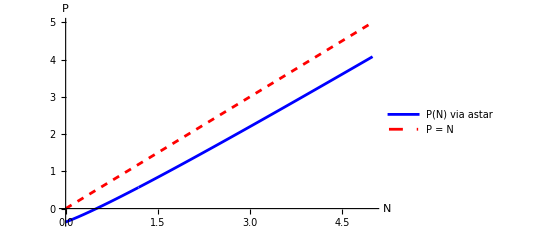

```mathematica
Plot[{P[n],n},{n,0,5},PlotStyle->{Blue,{Red,Dashed}},PlotLegends->{"P(N) via astar","P = N"},AxesLabel->{"N","P"}]
```